```mathematica
Exit[]
```

```mathematica
Directory[]
```

```mathematica
(* If you are not in the mm_lean directory already,  you should be *)
SetDirectory["~/proj/lean/mm_lean/src"];
```

```mathematica
(* Your Lean executable here *)
```

```mathematica
LeanExecutable=FileNameJoin[{$HomeDirectory,"lean/bin/lean"}];
```

```mathematica
<<"main.m"
<<"../_target/deps/mathematica/src/lean_form.m"
```

SocketListener[e8ff645b-c202-405a-ad97-523b7e0ae0cb]

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover", LeanExecutable]
```

fun (h : Prop) (h_1 : Prop) (h_2 : Prop) (h_3 : h -> h_1 -> h_2) (h_4 : and h h_1), (h_3 (and.left h h_1 h_4) (and.right h h_1 h_4))

```mathematica
ProveUsingLeanTactic[ForAllTyped[{p,q,r},Prop,Implies[Implies[p,Implies[q,r]],Implies[And[p,q],r]]],"mm_prover",LeanExecutable,True]
```

LeanLambda[LeanNameMkString["h", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_1", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_2", LeanNameAnonymous], BinderInfoDefault, LeanSort[LeanZeroLevel], LeanLambda[LeanNameMkString["h_3", LeanNameAnonymous], BinderInfoDefault, LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanPi[LeanNameMkString["a", LeanNameAnonymous], BinderInfoDefault, LeanVar[2], LeanVar[2]]], LeanLambda[LeanNameMkString["h_4", LeanNameAnonymous], BinderInfoDefault, LeanApp[LeanApp[LeanConst[LeanNameMkString["and", LeanNameAnonymous], LeanLevelListNil], LeanVar[3]], LeanVar[2]], LeanApp[LeanApp[LeanVar[1], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["left", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]], LeanApp[LeanApp[LeanApp[LeanConst[LeanNameMkString["right", LeanNameMkString["and", LeanNameAnonymous]], LeanLevelListNil], LeanVar[4]], LeanVar[3]], LeanVar[0]]]]]]]]

```mathematica
<<"natural_deduction_graphs.wl"
```

```mathematica
(*DiagramOfFormula[ForAll[{P},Not[And[Implies[P,Not[P]],Implies[Not[P],P]]]],{P},LeanExecutable]*)
```

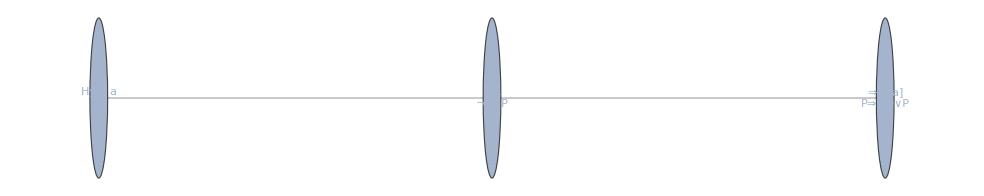

```mathematica
DiagramOfFormula[ForAll[{P,Q},Implies[P,Or[Not[Q],P]]],{P,Q},LeanExecutable]
```

```mathematica
(* <<"CICTranslate.m" *)
```

```mathematica
(* RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"elaborate",True]//ToExpression // CICTranslate *)
```

```mathematica
(* RunLeanTactic[LambdaFunction[Alpha,LambdaFunction[Typed[x,Alpha],x]],"type_check",True]//ToExpression // CICTranslate *)
```

```mathematica
(* RunLeanTactic[ForAllTyped[{s,t,u},set[nat],SetUnion[s,SetUnion[t,u]]==SetUnion[SetUnion[u,s],t]],"normalize_set_lemmas",LeanExecutable] *)
```

```mathematica
RunLeanTactic[ForAllTyped[{s,t},set[nat],SetInter[s,SetUnion[t,SetCompl[s]]]==SetInter[s,t]],"normalize_set_lemmas", LeanExecutable]
```

set_distrib_right : ∀ {α : Type ?} (s t u : set α), s ∩ (t ∪ u) = s ∩ t ∪ s ∩ u
set.union_empty : ∀ {α : Type ?} (a : set α), a ∪ ∅ = a
set.inter_compl_self : ∀ {α : Type ?} (s : set α), s ∩ -s = ∅

```mathematica
(* The example below requires you to be running a version of Lean with meta-floats. https://github.com/rlewis1988/lean/tree/floats/ *)
```

```mathematica
(* SelectLeanPremises[ForAllTyped[{x,y},real,Implies[x<y,Exists[{z},And[x<z, z<y]]]]] *)
```